# Leads connected to 1 - 10 and 1 to 10

# a1 and a2

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_]:= t*IdentityMatrix[10]
```

```mathematica
Clear[T]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,3,0.01]}]
```

```mathematica
leads[25]
```

{{{0.-0.848854 ⅈ,0.500319+0. ⅈ,0.+0.170564 ⅈ,-0.00148296+0. ⅈ,0.+0.0219777 ⅈ,0.00302035+0. ⅈ,0.+0.0116615 ⅈ,-0.00381066+0. ⅈ,0.+0.0000550464 ⅈ,0.0030296+0. ⅈ,0.+0.00421847 ⅈ,-0.00148449+0. ⅈ,0.+0.000330511 ⅈ,0.000363268+0. ⅈ,0.+0.000839972 ⅈ,-0.0000187093+0. ⅈ,0.+0.000473503 ⅈ,3.77068×10^-6+0. ⅈ,0.+0.000321694 ⅈ,-0.0000155762+0. ⅈ,0.+0.000184309 ⅈ,4.2504×10^-6+0. ⅈ,0.+0.000109971 ⅈ,-1.79988×10^-6+0. ⅈ,0.+0.0000334653 ⅈ},23,{0.+0.0000334653 ⅈ,23,0.-0.848854 ⅈ}},299,{1}}
 |  |  |  |

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+1]]]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Table[{x,25},{x,1,50,1}]
```

{{1,25},{2,25},{3,25},{4,25},{5,25},{6,25},{7,25},{8,25},{9,25},{10,25},{11,25},{12,25},{13,25},{14,25},{15,25},{16,25},{17,25},{18,25},{19,25},{20,25},{21,25},{22,25},{23,25},{24,25},{25,25},{26,25},{27,25},{28,25},{29,25},{30,25},{31,25},{32,25},{33,25},{34,25},{35,25},{36,25},{37,25},{38,25},{39,25},{40,25},{41,25},{42,25},{43,25},{44,25},{45,25},{46,25},{47,25},{48,25},{49,25},{50,25}}

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentration]=Table[SortBy[Join[RandomSample[Join[s[1,50,1,25]],concentration],RandomSample[Join[s[1,50,26,50]],total-concentration]],First],10000]
```

```mathematica
dist[50,10][[1]]
```

{{1,46},{1,48},{2,41},{4,38},{4,46},{5,30},{6,26},{7,39},{8,40},{8,42},{11,35},{12,50},{13,40},{13,43},{15,28},{17,28},{17,47},{18,26},{18,29},{18,48},{19,20},{19,29},{20,19},{22,48},{23,42},{25,28},{26,34},{28,11},{29,21},{31,42},{31,48},{32,21},{32,46},{32,48},{34,44},{35,25},{35,43},{36,41},{37,30},{37,42},{38,10},{40,46},{42,29},{42,32},{42,44},{42,47},{44,50},{47,10},{47,19},{47,24}}

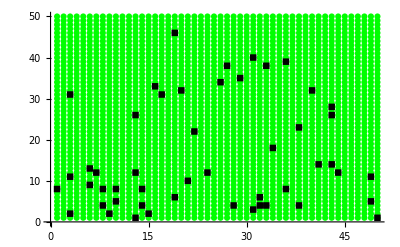

```mathematica
ListPlot[{Join[s[1,50,1,50]],dist[50,30][[1]]},PlotMarkers->Automatic,PlotStyle->{Green,Black}]
```

```mathematica
TLD[t_]:=Module[{sizeoflead=25},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,1,25}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
Clear[SLLEAD]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_]:=Module[{sizeoflead=25},Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].T[1,sizeoflead].SLLEAD[ω,sizeoflead].T[1,sizeoflead]].g[ω,0.0001,1,0]]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_]:= Module[{sizeoflead=25,abc=dist[total,concentration][[number]]},
recurs=Module[{J1= device1[ω]},
Do[
J1=Inverse[IdentityMatrix[50]-Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]].T[1,50].J1.T[1,50]].Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]],{unitcell,50}];J1=J1];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
(*Gnonlocallr=recurs.ConjugateTranspose[TLD[1]].ir;*)
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

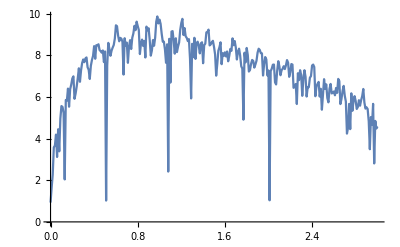

```mathematica
ListLinePlot[Table[{ω,CA[ω,0.0001,1,0,1,50,25,1]},{ω,Range[0,3,0.01]}]]
```

```mathematica
Table[Export["~/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_25_and_1_25/up_down/1_2/ϵ1_conc_"<>ToString[conc]<>"_.dat",Print[conc];Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,50,conc,n],{n,500}]]},{ω,Range[0,3,0.01]}]],{conc,5,45,5}]
```

5

10